# Estrategias de trading basadas en medias móviles

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Información de los paquetes cargados

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Cargar base de datos

```mathematica
DatedPrices[dates_,prices_]:=Transpose[{dates,prices}];
```

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","NASDAQ Composite","IPC","Nikkei 225"};
```

## Definición de estrategias

Funciones para pasar fecha a año porcentual y viceversa.

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

Calcula intersecciones entre medias móviles

```mathematica
RootsInRange[{f1_, f2_}, {t_, tmin_, tmax_}, opts___] := Module[
	{p, r, pts, x, f = Function[t, Evaluate[f1-f2]]},
	
	p = Plot[f[t], {t, tmin, tmax}];
	pts = Cases[First[p], Line[{x__}]->x, Infinity];
	r = Abs[Subtract@@Last@PlotRange[p]];
	pts = Map[First, Select[Split[pts, Sign[Last[#2]] == -Sign[Last[#1]] && Abs[Last[#2]-Last[#1]] < r/2&], Length[#1] == 2&], {2}];
	pts = (FindRoot[f[t]==0, {t, Sequence@@##}, Evaluate[Sequence@@FilterRules[{opts}, Options@FindRoot]]]&)/@pts;
	pts
];

RootsInRange[f1_==f2_, {t_, tmin_, tmax_}, opts___] := RootsInRange[{f1, f2}, {t, tmin, tmax}, opts];

Middle[l_List] := Part[l, Floor[Length[l]/2]];

VariableMovingAverage[l_List, f_] := Module[{subLists, windows}, 
	windows = Map[Ceiling[f[#]]&, l[[All, 2]]];
	subLists = DeleteCases[TakeList[l, Map[UpTo, windows]], {}];
	Map[{Middle[#[[All, 1]]], Mean[#[[All, 2]]]}&, subLists]
];

CrossoverTrading[datedPrices_, f1_, f2_] := Module[
	{
		numericDatePrices, avg1, avg2, datesMin, datesMax, priceInterpolation, avg1Interpolation, avg2Interpolation, 
		intersectionDates, x, firstInt, signals, buySignals, sellSignals, operations, return, result
	}, 
	numericDatePrices = MapAt[YearPercentual, datedPrices, {All,1}];

	avg1 = f1[numericDatePrices];
	avg2 = f2[numericDatePrices];
	datesMin = Max[{avg1[[1, 1]], avg2[[1, 1]]}];
	datesMax = Min[{avg1[[-1, 1]], avg2[[-1, 1]]}];

	priceInterpolation = Interpolation[numericDatePrices];
	avg1Interpolation = Interpolation[avg1];
	avg2Interpolation = Interpolation[avg2];
	
	intersectionDates = x /.RootsInRange[avg1Interpolation[x]==avg2Interpolation[x], {x, datesMin, datesMax}];
	
	(* Verificar que la primera intersección sea una operación de compra *)
	firstInt = First[intersectionDates];
	If[avg1Interpolation'[firstInt]-avg2Interpolation'[firstInt]<0, intersectionDates = Drop[intersectionDates, 1]];
	
	signals = Map[{DateFromYearPercentual[#], priceInterpolation[#]}&, intersectionDates];
	buySignals = signals[[1;;-1;;2]];
	sellSignals = signals[[2;;-1;;2]];

	operations = Partition[priceInterpolation[intersectionDates], 2];
	return = Total[operations[[All, 2]]-operations[[All, 1]]];

	result = <|"BuySignals"->buySignals, "SellSignals"->sellSignals, "Return"->return|>;
	Return[result];
];
```

### Idea del algoritmo

Tomamos 20 muestras de precios.

```mathematica
datos = Take[First[database]["DatedPrices"],20]
```

{{Day: Fri 8 Nov 1991,1606.2},{Day: Mon 11 Nov 1991,1609},{Day: Tue 12 Nov 1991,1621.2},{Day: Wed 13 Nov 1991,1623.2},{Day: Thu 14 Nov 1991,1621},{Day: Fri 15 Nov 1991,1629.4},{Day: Mon 18 Nov 1991,1611.9},{Day: Tue 19 Nov 1991,1599.1},{Day: Thu 21 Nov 1991,1598.1},{Day: Fri 22 Nov 1991,1600.3},{Day: Mon 25 Nov 1991,1589.2},{Day: Tue 26 Nov 1991,1602.9},{Day: Wed 27 Nov 1991,1586.2},{Day: Thu 28 Nov 1991,1588.2},{Day: Fri 29 Nov 1991,1566.6},{Day: Mon 2 Dec 1991,1545.4},{Day: Tue 3 Dec 1991,1546.8},{Day: Wed 4 Dec 1991,1561},{Day: Thu 5 Dec 1991,1553.4},{Day: Fri 6 Dec 1991,1558.2}}

Para poder computar una media móvil es necesario pasar las fechas a fechas porcentuales.

```mathematica
datosPorcentuales = MapAt[YearPercentual, datos, {All,1}]
```

{{1991.85,1606.2},{1991.86,1609},{1991.86,1621.2},{1991.87,1623.2},{1991.87,1621},{1991.87,1629.4},{1991.88,1611.9},{1991.88,1599.1},{1991.89,1598.1},{1991.89,1600.3},{1991.9,1589.2},{1991.9,1602.9},{1991.9,1586.2},{1991.91,1588.2},{1991.91,1566.6},{1991.92,1545.4},{1991.92,1546.8},{1991.92,1561},{1991.93,1553.4},{1991.93,1558.2}}

Con esto se puede calcular la media móvil con diferentes ventanas

```mathematica
MovingAverage[datosPorcentuales,5]
```

{{1991.86,1616.12},{1991.87,1620.76},{1991.87,1621.34},{1991.87,1616.92},{1991.88,1611.9},{1991.88,1607.76},{1991.89,1599.72},{1991.89,1597.92},{1991.9,1595.34},{1991.9,1593.36},{1991.9,1586.62},{1991.91,1577.86},{1991.91,1566.64},{1991.92,1561.6},{1991.92,1554.64},{1991.92,1552.96}}

```mathematica
MovingAverage[datosPorcentuales,10]
```

{{1991.87,1611.94},{1991.88,1610.24},{1991.88,1609.63},{1991.88,1606.13},{1991.89,1602.63},{1991.89,1597.19},{1991.9,1588.79},{1991.9,1582.28},{1991.91,1578.47},{1991.91,1574.},{1991.91,1569.79}}

El usuario puede introducir la media móvil deseada al algoritmo. Aquí se utiliza la media móvil stándard en la primera función y una media móvil exponencial en la segunda función.

```mathematica
CrossoverTrading[
Take[First[database]["DatedPrices"],100],
MovingAverage[#,20]&,
ExponentialMovingAverage[#,40]&
]
```

<|BuySignals→{{Day: Sat 15 Feb 1992,1673.56}},SellSignals→{{Day: Wed 18 Mar 1992,1726.6}},Return→53.0394|>

### Resultados

```mathematica
market = First[database];
```

```mathematica
strategyResults = CrossoverTrading[
market["DatedPrices"],
MovingAverage[#,20]&,
MovingAverage[#,40]&
];
```

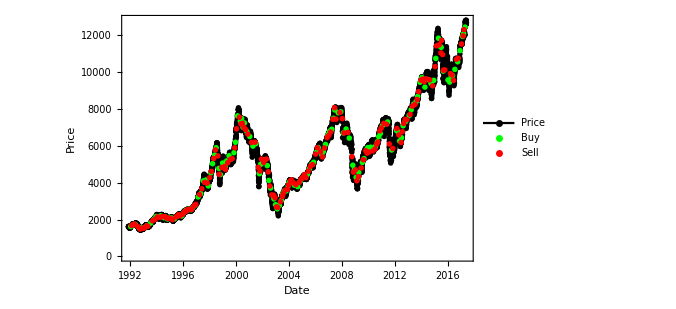

```mathematica
DateListPlot[
{market["DatedPrices"],strategyResults["BuySignals"],strategyResults["SellSignals"]},
Joined->{True,False,False},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->{"Price","Buy","Sell"},
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,Green,Red}
]
```